What is the terminal velocity of a SmartDart?

### from videos you can measure the length of the dart, and compare posiiton in 2 frames

```mathematica
(*CONSTANTS*)
AreaProj =π (0.06/2)^2 ;(*area of the dart, m^2, 60mm in diameter*)
Cd = 0.4; (*0.47 for sphere, 0.04 for streamlined body*)
m = 0.2; (*kg*)
ρ = 1.225; (*density of air kg/m3*)
g= 9.8; (*m/s2*)
```

```mathematica
Vt =√((2 m g)/(ρ AreaProj Cd)) (*Terminal Velocity, in m/s*)
```

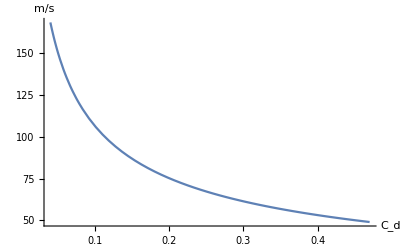

```mathematica
Plot[√((2 m g)/(ρ AreaProj Cd)),{Cd,0.04,0.47},PlotRange->All, AxesOrigin->{0,0},AxesLabel->{"C_d","m/s"}]
```

Solve to get velocity as a function of time

```mathematica
DSolve[{v'[t]==b - v[t]^2 a,v[0]==0},v,t] (* a= 1/2 ρ AreaProj Cd, b = mg, terminal velocity = (√b)/(√a)*)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v→Function[{t},(√b Tanh[√a √b t])/(√a)]}}

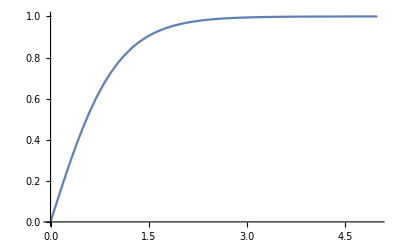

```mathematica
Plot[Tanh[ t],{t,0,5},PlotRange->All]
```

Solve to get position as a function of time

```mathematica
DSolve[{p''[t]==b - p'[t]^2 a,p[0]==0,p'[0]==0},p,t]
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is 1 - Cosh[√a\ √b\ C[1]]^2 == 0.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{p→Function[{t},Log[Cosh[√a √b t]]/a]},{p→Function[{t},(-ⅈ π+Log[Cosh[√a √b (-(ⅈ π)/(√a √b)+t)]])/a]}}

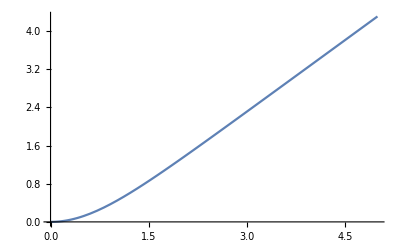

```mathematica
Plot[Log[Cosh[ t]],{t,0,5}]
```

Falling object reaches 90% speed at time

```mathematica
Solve[Tanh[√a √b t]==9/10,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→ArcTanh[9/10]/(√a √b)}}

Falling object reaches 90% speed when it falls from what height?

```mathematica
FullSimplify[Log[Cosh[√a √b ArcTanh[9/10]/(√a √b)]]/a]
```

```mathematica
Log[100/19]/(2 a)/.a-> 1/2 ρ AreaProj Cd
```

```mathematica
4794.804185263211 if Cd = 0.1
```

```mathematica
Log[100/19]/(2 a)/.a-> 1/2 ρ AreaProj Cd
```

1198.7

Compare with Cd

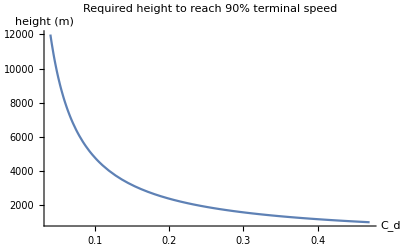

```mathematica
Plot[Log[100/19]/(2 a)/.a-> 1/2 ρ AreaProj Cd,{ Cd,0.04,0.47},PlotRange->All,

PlotLabel->"Required height to reach 90% terminal speed",AxesLabel->{"C_d","height (m)"}]
```

Compare analytic to numeric solution (they match, so no need for numeric solution)

```mathematica
s=NDSolve[{y''[t]== m g -1/2 y'[t]^2 ρ AreaProj Cd,y[0]==0,y'[0]==0},y,{t,0,200}]
```

{{y→InterpolatingFunction[{{0., 200.}}, <>]}}

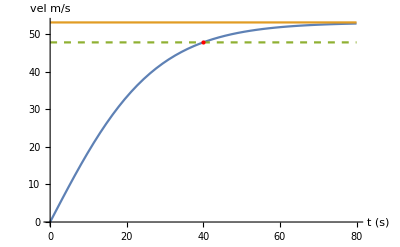

```mathematica
t90 = ArcTanh[9/10]/(√a √b)/.{a->  1/2 ρ AreaProj Cd, b-> m g};
Plot[{Evaluate[y'[t]/.s],√((2 m g)/(ρ AreaProj Cd)),0.9*√((2 m g)/(ρ AreaProj Cd))},{t,0,80},PlotRange->All,PlotStyle->{Automatic,Automatic,Dashed},
Epilog->{PointSize->Large,Red, Point[{t90,0.9*√((2 m g)/(ρ AreaProj Cd))}]}, AxesLabel->{"t (s)","vel m/s"}]
```

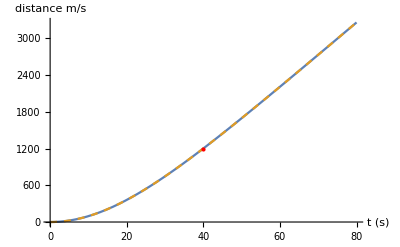

```mathematica
Plot[{Evaluate[y[t]/.s],Log[Cosh[√a √b t]]/a/.{a->  1/2 ρ AreaProj Cd, b-> m g}},{t,0,80},PlotRange->All,PlotStyle->{Automatic,Dashed},
Epilog->{PointSize->Large,Red, Point[{t90,Log[Cosh[√a √b t90]]/a/.{a->  1/2 ρ AreaProj Cd, b-> m g}}]},

AxesLabel->{"t (s)","distance m/s"}]
```